# Computations for an American Mathematical Monthly Article

```mathematica
Clear["Global`*"]
```

## Trapezoidal Rule

```mathematica
traprule[f_,N_]:=((f[0]+f[1])/2+Sum[f[i/N],{i,1,N-1}])/N
```

```mathematica
simprule[f_,Nov2_]:=(f[0]+f[1]+4Sum[f[(i-1/2)/Nov2],{i,1,Nov2}]+2Sum[f[i/Nov2],{i,1,Nov2-1}])/(6Nov2)
```

```mathematica
xf[x_]:=x-1/2
ixf=Integrate[xf[x],{x,0,1}]
errxf=Simplify[ixf-{traprule[xf,N],simprule[xf,N/2]}]
```

0

{0,0}

```mathematica
x2f[x_]:=(x-1/2)^2
ix2f=Integrate[x2f[x],{x,0,1}]
errx2f=Simplify[ix2f-{traprule[x2f,N],simprule[x2f,N/2]}]
errhatx2f=Simplify[traprule[x2f,N]-traprule[x2f,N/2],Assumptions -> N/2∈Integers]
```

1/12

{-1/(6 N^2),0}

-1/(2 N^2)

```mathematica
x3f[x_]:=(x-1/2)^3
ix3f=Integrate[x3f[x],{x,0,1}]
errx3f=Simplify[ix3f-{traprule[x3f,N],simprule[x3f,N/2]}]
```

0

{0,0}

```mathematica
x4f[x_]:=(x-1/2)^4
ix4f=Integrate[x4f[x],{x,0,1}]
errx4f=Simplify[ix4f-{traprule[x4f,N],simprule[x4f,N/2]}]
```

1/80

{(2-5 N^2)/(60 N^4),-2/(15 N^4)}

```mathematica
x1absf[x_]:=Abs[x-1/2]
ix1absf=Integrate[x1absf[x],{x,0,1}]
errx1absf={Simplify[ix1absf-{traprule[x1absf,N],simprule[x1absf,N/2]},Assumptions -> N/4∈Integers],Simplify[ix1absf-{traprule[x1absf,N],simprule[x1absf,N/2]},Assumptions -> (N+2)/4∈Integers]}
```

1/4

{{0,0},{0,1/(3 N^2)}}

```mathematica
x3absf[x_]:=(Abs[x-1/2])^3
ix3absf=Integrate[x3absf[x],{x,0,1}]
errx3absf={Simplify[ix3absf-{traprule[x3absf,N],simprule[x3absf,N/2]},Assumptions -> N/4∈Integers],Simplify[ix3absf-{traprule[x3absf,N],simprule[x3absf,N/2]},Assumptions -> (N+2)/4∈Integers]}
errhatx3absf={Simplify[Simplify[traprule[x3absf,4M]-traprule[x3absf,2M],Assumptions -> M∈Integers]/. M -> N/4],Simplify[Simplify[traprule[x3absf,4M+2]-traprule[x3absf,2M+1],Assumptions -> M∈Integers]/. M -> (N-2)/4]}
```

1/32

{{-1/(8 N^2),0},{-1/(8 N^2),-1/(6 N^4)}}

{-3/(8 N^2),(4-3 N^2)/(8 N^4)}

## Gaussian Distribution Example

```mathematica
phi[x_]=Exp[-x^2/2]/Sqrt[2*Pi]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
dphi[x_]=D[phi[x],x]
```

-(ⅇ^(-x^2/2) x)/(√(2 π))

```mathematica
Maximize[{dphi[x],x≥0,x≤1},x]
```

{0,{x→0}}

```mathematica
Minimize[{dphi[x],x≥0,x≤1},x]
```

{-1/(√(2 ⅇ π)),{x→1}}

## Spiky Function Example

### Spiky Function and Its Derivatives

```mathematica
fhump[x_]=1+60BernoulliB[4,x]
```

1+60 (-1/30+x^2-2 x^3+x^4)

```mathematica
Integrate[fhump[x],{x,0,1}]
```

1

```mathematica
Simplify[fhump[1/2]] (*Maximum value of fpc*)
```

11/4

```mathematica
fhump[0]
```

-1

```mathematica
dfhump[x_]=240BernoulliB[3,x]
```

240 (x/2-(3 x^2)/2+x^3)

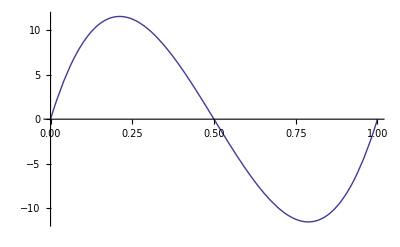

```mathematica
Plot[dfhump[x],{x,0,1}]
```

```mathematica
ddfhump[x_]=720BernoulliB[2,x]
```

720 (1/6-x+x^2)

```mathematica
dddfhump[x_]=1440BernoulliB[1,x]
```

1440 (-1/2+x)

### Total Variation of First Derivative of Fluky Function

```mathematica
noded=Solve[ddfhump[x]==0,x]
```

{{x→1/6 (3-√3)},{x→1/6 (3+√3)}}

```mathematica
nodedx=Simplify[x/.noded]
```

{1/6 (3-√3),1/6 (3+√3)}

```mathematica
nodedx={0,nodedx[[1]],nodedx[[2]],1}
```

{0,1/6 (3-√3),1/6 (3+√3),1}

```mathematica
nodedy=Simplify[dfhump[nodedx]]
```

{0,20/(√3),-20/(√3),0}

```mathematica
totvardfhump=Sum[Abs[Differences[nodedy]][[i]],{i,1,3}]
```

80/(√3)

### Total Variation of Second Derivative of Fluky Function

```mathematica
nodeddx={0,1/2,1}
```

{0,1/2,1}

```mathematica
nodeddy=Simplify[ddfhump[nodeddx]]
```

{120,-60,120}

```mathematica
totvarddfhump=Sum[Abs[Differences[nodeddy]][[i]],{i,1,2}]
```

360

## Fluky Function Example

### Fluky Function and Its Derivatives

```mathematica
foolB[x_,N_]=Simplify[1-15*N^2*(BernoulliB[2,x]+N^2 BernoulliB[4,x])]
```

1-15 N^2 (1/6-x+x^2+N^2 (-1/30+x^2-2 x^3+x^4))

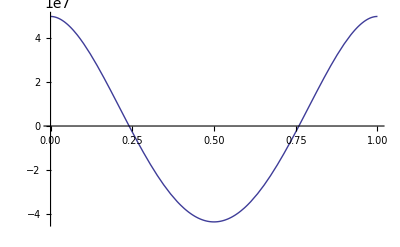

```mathematica
Plot [foolB[x,100],{x,0,1}]
```

```mathematica
Integrate[foolB[x,N],{x,0,1}]
```

1

```mathematica
fB2[x_]=BernoulliB[2,x]
Simplify[traprule[fB2,N]]
```

1/6-x+x^2

1/(6 N^2)

```mathematica
fB4[x_]=BernoulliB[4,x]
Simplify[traprule[fB4,N]]
```

-1/30+x^2-2 x^3+x^4

-1/(30 N^4)

```mathematica
f4[x_]=x^4
Simplify[traprule[f4,N]]
```

x^4

1/30 (6-1/N^4+10/N^2)

```mathematica
ffoolB[x_]=foolB[x,N]
```

1-15 N^2 (1/6-x+x^2+N^2 (-1/30+x^2-2 x^3+x^4))

1-15 N^2 (1/6-x+x^2+N^2 (-1/30+x^2-2 x^3+x^4))

```mathematica
Simplify[traprule[ffoolB,N]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/2]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/4]]
```

89

```mathematica
dfoolB[x_,N]=Simplify[-30*N^2*(BernoulliB[1,x]+2 N^2BernoulliB[3,x])]
```

-15 N^2 (-1+2 x) (1+2 N^2 (-1+x) x)

```mathematica
ddfoolB[x_,N]=Simplify[-30*N^2*(1+6 N^2BernoulliB[2,x])]
```

-30 N^2 (1+N^2 (1-6 x+6 x^2))

```mathematica
dddfoolB[x_,N]=Simplify[-360* N^4BernoulliB[1,x]]
```

-180 N^4 (-1+2 x)

```mathematica
ddddfoolB[x_,N]=-360* N^4
```

-360 N^4

### Total Variation of Fluky Function

```mathematica
node=Solve[dfoolB[x,N]==0,x]
```

{{x→1/2},{x→(N^2-√(-2 N^2+N^4))/(2 N^2)},{x→(N^2+√(-2 N^2+N^4))/(2 N^2)}}

```mathematica
nodex=x/.node
```

{1/2,(N^2-√(-2 N^2+N^4))/(2 N^2),(N^2+√(-2 N^2+N^4))/(2 N^2)}

```mathematica
nodex={0,nodex[[2]],nodex[[1]],nodex[[3]],1}
```

{0,(N^2-√(-2 N^2+N^4))/(2 N^2),1/2,(N^2+√(-2 N^2+N^4))/(2 N^2),1}

```mathematica
nodey=Simplify[foolB[nodex,N]]
```

{1/2 (2-5 N^2+N^4),1/4 (19-10 N^2+2 N^4),1+(5 N^2)/4-(7 N^4)/16,1/4 (19-10 N^2+2 N^4),1/2 (2-5 N^2+N^4)}

```mathematica
absdify=Simplify[Abs[Differences[nodey]]]
```

{15/4,15/16 Abs[-2+N^2]^2,15/16 Abs[-2+N^2]^2,15/4}

```mathematica
totvarfool=Expand[Simplify[Sum[absdify[[i]],{i,1,4}],Assumptions -> N≥ 2]]
```

15-(15 N^2)/2+(15 N^4)/8

### Total Variation of First Derivative of Fluky Function

```mathematica
noded=Solve[ddfoolB[x,N]==0,x]
```

{{x→(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2)},{x→(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2)}}

```mathematica
nodedx=x/.noded
```

{(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2),(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2)}

```mathematica
nodedx={0,nodedx[[1]],nodedx[[2]],1}
```

{0,(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2),(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2),1}

```mathematica
nodedy=Simplify[dfoolB[nodedx,N]]
```

{15 N^2,-(5 (N^2 (-2+N^2))^(3/2))/(√3 N^2),(5 (N^2 (-2+N^2))^(3/2))/(√3 N^2),-15 N^2}

```mathematica
absdifdy=Simplify[Abs[Differences[nodedy]],Assumptions -> N≥2]
```

{5/3 N (9 N+√3 (-2+N^2)^(3/2)),(10 N (-2+N^2)^(3/2))/(√3),5/3 N (9 N+√3 (-2+N^2)^(3/2))}

```mathematica
totvardfool=Simplify[Sum[absdifdy[[i]],{i,1,3}],Assumptions -> N≥2]
```

10/3 N (9 N+2 √3 (-2+N^2)^(3/2))

```mathematica
conetaufool=Simplify[totvardfool/totvarfool]
```

(16 N (9 N+2 √3 (-2+N^2)^(3/2)))/(9 (8-4 N^2+N^4))

### Total Variation of Second Derivative of Fluky Function

```mathematica
nodedd=Solve[dddfoolB[x,N]==0,x]
```

{{x→1/2}}

```mathematica
nodeddx=x/.nodedd
```

{1/2}

```mathematica
nodeddx={0,nodeddx[[1]],1}
```

{0,1/2,1}

```mathematica
nodeddy=Simplify[ddfoolB[nodeddx,N]]
```

{-30 N^2 (1+N^2),15 N^2 (-2+N^2),-30 N^2 (1+N^2)}

```mathematica
absdifddy=Simplify[Abs[Differences[nodeddy]]]
```

{45 Abs[N]^4,45 Abs[N]^4}

```mathematica
totvarddfool=Simplify[Sum[absdifddy[[i]],{i,1,2}],Assumptions -> N∈Integers]
```

90 N^4

### A Slightly Different Function

```mathematica
badfoolB2[x_,N_]=15*N^2BernoulliB[2,x]
```

15 N^2 (1/6-x+x^2)

```mathematica
Integrate[badfoolB2[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB2[i/N,N],{i,0,N-1}]/N
```

5/2

```mathematica
trapNov2=Sum[badfoolB2[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

10

```mathematica
errhat=(trapN - trapNov2)/3
```

-5/2

```mathematica
badfoolB4[x_,N_]=15*N^4BernoulliB[4,x]
```

15 N^4 (-1/30+x^2-2 x^3+x^4)

```mathematica
Integrate[badfoolB4[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB4[i/N,N],{i,0,N-1}]/N
```

-1/2

```mathematica
trapNov2=Sum[badfoolB4[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

-8

```mathematica
errhat=(trapN - trapNov2)/3
```

5/2

## Alternative Fluky Function Example

### Fluky Function and Its Derivatives

```mathematica
foolB[x_,N_]=Simplify[1-60*N^2*(BernoulliB[2,x/2]+4N^2 BernoulliB[4,x/2])]
```

1-5 N^2 (2-6 x+3 x^2)+N^4 (8-60 x^2+60 x^3-15 x^4)

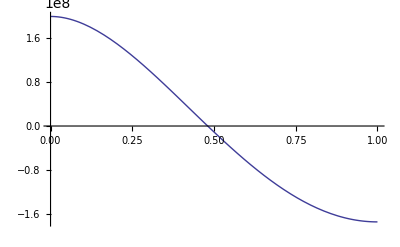

```mathematica
Plot [foolB[x,100],{x,0,1}]
```

```mathematica
Integrate[foolB[x,N],{x,0,1}]
```

1

```mathematica
fB2[x_]=BernoulliB[2,x/2]
```

1/6-x/2+x^2/4

```mathematica
Simplify[traprule[fB2,N]]
```

1/(24 N^2)

```mathematica
Simplify[traprule[fB2,N/2]]
```

1/(6 N^2)

```mathematica
fB4[x_]=BernoulliB[4,x/2]
```

-1/30+x^2/4-x^3/4+x^4/16

```mathematica
Simplify[traprule[fB4,N]]
```

-1/(480 N^4)

```mathematica
Simplify[traprule[fB4,N/2]]
```

-1/(30 N^4)

```mathematica
Simplify[traprule[fB2,N]]+4N^2 Simplify[traprule[fB4,N]]
```

1/(30 N^2)

```mathematica
ffoolB[x_]=foolB[x,N]
```

1-5 N^2 (2-6 x+3 x^2)+N^4 (8-60 x^2+60 x^3-15 x^4)

```mathematica
BernoulliB[4,x]
```

-1/30+x^2-2 x^3+x^4

```mathematica
Simplify[traprule[ffoolB,N]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/2]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/4]]
```

89

```mathematica
dfoolB[x_,N]=Simplify[-120*N^2*(BernoulliB[1,x]+4N^2(BernoulliB[3,x/2]-1))]
```

-60 N^2 (-1+2 x+N^2 (-8+2 x-3 x^2+x^3))

```mathematica
ddfoolB[x_,N]=Simplify[-30*N^2*(1+24 N^2BernoulliB[2,x/2])]
```

-30 N^2 (1+2 N^2 (2-6 x+3 x^2))

```mathematica
dddfoolB[x_,N]=Simplify[-720* N^4BernoulliB[1,x/2]]
```

-360 N^4 (-1+x)

```mathematica
ddddfoolB[x_,N]=-360* N^4
```

-360 N^4

### Total Variation of Fluky Function

```mathematica
node=Solve[dfoolB[x,N]==0,x]
```

{{x→1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2)},{x→1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)},{x→1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)}}

```mathematica
nodex=x/.node
```

{1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2),1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)}

```mathematica
nodex={0,nodex[[2]],nodex[[1]],nodex[[3]],1}
```

{0,1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2),1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1}

```mathematica
nodey=Simplify[foolB[nodex,N]]
```

{1-10 N^2+2 N^4,1-5 N^2 (2-6 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+3 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2)+N^4 (2-15 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2+15 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^3-15/4 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^4),1-(5 (12 3^(1/3) N^4-48 3^(1/3) N^6+48 3^(1/3) N^8-12 N^2 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+12 N^4 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+3^(2/3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(4/3)))/(12 N^2 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+N^4 (2-15 (1+1/(2 3^(2/3) N^2)(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(-1+2 N^2)/(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))^2+15 (1+1/(2 3^(2/3) N^2)(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(-1+2 N^2)/(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))^3-15/4 (1+1/(2 3^(2/3) N^2)(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(-1+2 N^2)/(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))^4),1-5 N^2 (2-6 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+3 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2)+N^4 (2-15 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2+15 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^3-15/4 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^4),1+5 N^2-(7 N^4)/4}

```mathematica
absdify=Simplify[Abs[Differences[nodey]]]
```

{Abs[10 N^2-2 N^4-5 N^2 (2-6 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+3 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2)+N^4 (2-15 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2+15 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^3-15/4 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^4)],5/64 3^(1/6) Abs[(1117824 (ⅈ+√3) N^10-220800 (ⅈ+√3) N^12-3 3^(1/6) (-ⅈ+√3) √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+24 N^6 (ⅈ+√3-96 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-32 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-54 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+18 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+3 N^4 (56 ⅈ+56 √3+3864 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+1288 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-111 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+37 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+56 N^8 (-1197 ⅈ-1197 √3+492 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)-164 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+4 N^2 (-90 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-30 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+21 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)-24 ⅈ 3^(1/6) √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)-7 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+24 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(4/3)],5/64 3^(1/6) Abs[(1117824 (-ⅈ+√3) N^10-220800 (-ⅈ+√3) N^12-3 3^(1/6) (ⅈ+√3) √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+24 N^6 (-ⅈ+√3-96 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+32 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-54 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)-18 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+3 N^4 (-56 ⅈ+56 √3+3864 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-1288 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-111 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)-37 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+56 N^8 (1197 ⅈ-1197 √3+492 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+164 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+4 N^2 (-90 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+30 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+21 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+24 ⅈ 3^(1/6) √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+7 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+24 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(4/3)],1/(4608 3^(1/3))5 Abs[((2 3^(1/3) (ⅈ+√3) N^2-4 3^(1/3) (ⅈ+√3) N^4+(-ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))^2 (12 3^(1/3) N^4+12 ⅈ 3^(5/6) N^4-48 3^(1/3) N^6-48 ⅈ 3^(5/6) N^6+48 3^(1/3) N^8+48 ⅈ 3^(5/6) N^8-264 N^2 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+96 N^4 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)-3 ⅈ 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(4/3)+3^(2/3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(4/3)))/(N^4 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(4/3))]}

```mathematica
totvarfool=Expand[Simplify[Sum[absdify[[i]],{i,1,4}],Assumptions -> N≥ 2]]
```

1/(4608 3^(1/3))5 Abs[((2 3^(1/3) (ⅈ+√3) N^2-4 3^(1/3) (ⅈ+√3) N^4+(-ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))^2 (12 3^(1/3) N^4+12 ⅈ 3^(5/6) N^4-48 3^(1/3) N^6-48 ⅈ 3^(5/6) N^6+48 3^(1/3) N^8+48 ⅈ 3^(5/6) N^8-264 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+96 N^6 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)-3 ⅈ 3^(1/6) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(4/3)+3^(2/3) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(4/3)))/(N^8 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(4/3))]+(5 3^(1/6) Abs[1117824 (ⅈ+√3) N^10-220800 (ⅈ+√3) N^12-3 3^(1/6) (-ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+24 N^6 (ⅈ+√3-32 ⅈ (-3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+18 ⅈ 3^(1/6) (3 ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+3 N^4 (56 (ⅈ+√3)+1288 (3+ⅈ √3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+37 ⅈ 3^(1/6) (3 ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+4 N^2 (-30 ⅈ (-3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+7 3^(1/6) (3-ⅈ √3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+24 3^(1/6) (-ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+56 N^8 (-1197 ⅈ-1197 √3+492 3^(1/6) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3)-164 ⅈ 3^(2/3) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3))])/(64 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(4/3))+(5 3^(1/6) Abs[1117824 (-ⅈ+√3) N^10-220800 (-ⅈ+√3) N^12-3 3^(1/6) (ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+24 N^6 (-ⅈ+√3+32 ⅈ (3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)-18 ⅈ 3^(1/6) (-3 ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+3 N^4 (56 (-ⅈ+√3)+1288 (3-ⅈ √3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)-37 ⅈ 3^(1/6) (-3 ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+4 N^2 (30 ⅈ (3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+7 3^(1/6) (3+ⅈ √3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+24 3^(1/6) (ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+56 N^8 (1197 ⅈ-1197 √3+492 3^(1/6) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+164 ⅈ 3^(2/3) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3))])/(64 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(4/3))+Abs[10 N^2-2 N^4-5 N^2 (2-6 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+3 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2)+N^4 (2-15 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2+15 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^3-15/4 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^4)]

### Total Variation of First Derivative of Fluky Function

```mathematica
noded=Solve[ddfoolB[x,N]==0,x]
```

{{x→(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2)},{x→(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2)}}

```mathematica
nodedx=x/.noded
```

{(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2),(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2)}

```mathematica
nodedx={0,nodedx[[1]],nodedx[[2]],1}
```

{0,(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2),(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2),1}

```mathematica
nodedy=Simplify[dfoolB[nodedx,N]]
```

{15 N^2 (1+32 N^2),-5/3 (-288 N^4-2 √6 √(N^2 (-1+2 N^2))+N^2 (9+4 √6 √(N^2 (-1+2 N^2)))),5/3 (288 N^4-2 √6 √(N^2 (-1+2 N^2))+N^2 (-9+4 √6 √(N^2 (-1+2 N^2)))),15 N^2 (-1+32 N^2)}

```mathematica
absdifdy=Simplify[Abs[Differences[nodedy]],Assumptions -> N≥2]
```

{10/3 N (9 N-√(-6+12 N^2)+2 N^2 √(-6+12 N^2)),20 √(2/3) N (-1+2 N^2)^(3/2),10 √(2/3) N (-1+2 N^2)^(3/2)}

```mathematica
totvardfool=Simplify[Sum[absdifdy[[i]],{i,1,3}],Assumptions -> N≥2]
```

10/3 N (9 N-4 √(-6+12 N^2)+8 N^2 √(-6+12 N^2))

```mathematica
conetaufool=Simplify[totvardfool/totvarfool]
```

(10 N (9 N-4 √(-6+12 N^2)+8 N^2 √(-6+12 N^2)))/(3 (1/(4608 3^(1/3))5 Abs[((2 3^(1/3) (ⅈ+√3) N^2-4 3^(1/3) (ⅈ+√3) N^4+(-ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))^2 (12 3^(1/3) N^4+12 ⅈ 3^(5/6) N^4-48 3^(1/3) N^6-48 ⅈ 3^(5/6) N^6+48 3^(1/3) N^8+48 ⅈ 3^(5/6) N^8-264 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+96 N^6 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)-3 ⅈ 3^(1/6) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(4/3)+3^(2/3) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(4/3)))/(N^8 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(4/3))]+(5 3^(1/6) Abs[1117824 (ⅈ+√3) N^10-220800 (ⅈ+√3) N^12-3 3^(1/6) (-ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+24 N^6 (ⅈ+√3-32 ⅈ (-3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+18 ⅈ 3^(1/6) (3 ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+3 N^4 (56 (ⅈ+√3)+1288 (3+ⅈ √3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+37 ⅈ 3^(1/6) (3 ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+4 N^2 (-30 ⅈ (-3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+7 3^(1/6) (3-ⅈ √3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+24 3^(1/6) (-ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+56 N^8 (-1197 ⅈ-1197 √3+492 3^(1/6) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3)-164 ⅈ 3^(2/3) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3))])/(64 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(4/3))+(5 3^(1/6) Abs[1117824 (-ⅈ+√3) N^10-220800 (-ⅈ+√3) N^12-3 3^(1/6) (ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+24 N^6 (-ⅈ+√3+32 ⅈ (3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)-18 ⅈ 3^(1/6) (-3 ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+3 N^4 (56 (-ⅈ+√3)+1288 (3-ⅈ √3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)-37 ⅈ 3^(1/6) (-3 ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+4 N^2 (30 ⅈ (3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+7 3^(1/6) (3+ⅈ √3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+24 3^(1/6) (ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+56 N^8 (1197 ⅈ-1197 √3+492 3^(1/6) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+164 ⅈ 3^(2/3) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3))])/(64 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(4/3))+Abs[10 N^2-2 N^4-5 N^2 (2-6 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+3 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2)+N^4 (2-15 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2+15 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^3-15/4 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^4)]))

### Total Variation of Second Derivative of Fluky Function

```mathematica
nodedd=Solve[dddfoolB[x,N]==0,x]
```

{{x→1}}

```mathematica
nodeddx=x/.nodedd
```

{1}

```mathematica
nodeddx={0,nodeddx[[1]],1}
```

{0,1,1}

```mathematica
nodeddy=Simplify[ddfoolB[nodeddx,N]]
```

{-30 N^2 (1+4 N^2),30 N^2 (-1+2 N^2),30 N^2 (-1+2 N^2)}

```mathematica
absdifddy=Simplify[Abs[Differences[nodeddy]]]
```

{180 Abs[N]^4,0}

```mathematica
totvarddfool=Simplify[Sum[absdifddy[[i]],{i,1,2}],Assumptions -> N∈Integers]
```

180 N^4

### A Slightly Different Function

```mathematica
badfoolB2[x_,N_]=15*N^2BernoulliB[2,x]
```

15 N^2 (1/6-x+x^2)

```mathematica
Integrate[badfoolB2[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB2[i/N,N],{i,0,N-1}]/N
```

5/2

```mathematica
trapNov2=Sum[badfoolB2[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

10

```mathematica
errhat=(trapN - trapNov2)/3
```

-5/2

```mathematica
badfoolB4[x_,N_]=15*N^4BernoulliB[4,x]
```

15 N^4 (-1/30+x^2-2 x^3+x^4)

```mathematica
Integrate[badfoolB4[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB4[i/N,N],{i,0,N-1}]/N
```

-1/2

```mathematica
trapNov2=Sum[badfoolB4[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

-8

```mathematica
errhat=(trapN - trapNov2)/3
```

5/2

## Another Alternative Fluky Function Example

### Fluky Function and Its Derivatives

```mathematica
foolB[x_,N_]=Simplify[1-15*N^2*(BernoulliB[2,x]+N^2 (16BernoulliB[4,x/2]-BernoulliB[1,x]))]
```

1-5/2 N^2 (1-6 x+6 x^2)+N^4 (1/2+15 x-60 x^2+60 x^3-15 x^4)

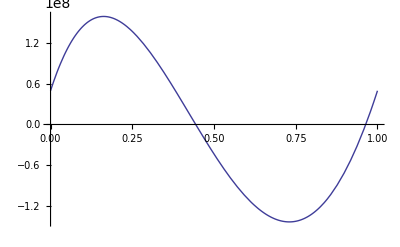

```mathematica
Plot [foolB[x,100],{x,0,1}]
```

```mathematica
Integrate[foolB[x,N],{x,0,1}]
```

1

```mathematica
ffoolB[x_]=foolB[x,N]
```

1-5/2 N^2 (1-6 x+6 x^2)+N^4 (1/2+15 x-60 x^2+60 x^3-15 x^4)

```mathematica
BernoulliB[4,x]
```

-1/30+x^2-2 x^3+x^4

```mathematica
Simplify[traprule[ffoolB,N]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/2]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/4]]
```

89

```mathematica
dfoolB[x_,N]=Simplify[-30*N^2*(BernoulliB[1,x]+16N^2(BernoulliB[3,x/2]-1))]
```

-30 N^2 (-1/2+x+2 N^2 (-8+2 x-3 x^2+x^3))

```mathematica
ddfoolB[x_,N]=Simplify[-30*N^2*(1+24 N^2BernoulliB[2,x/2])]
```

-30 N^2 (1+2 N^2 (2-6 x+3 x^2))

```mathematica
dddfoolB[x_,N]=Simplify[-720* N^4BernoulliB[1,x/2]]
```

-360 N^4 (-1+x)

```mathematica
ddddfoolB[x_,N]=-360* N^4
```

-360 N^4

### Total Variation of Fluky Function

```mathematica
node=Solve[dfoolB[x,N]==0,x]
```

{{x→1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2)},{x→1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)},{x→1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)}}

```mathematica
nodex=x/.node
```

{1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2),1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)}

```mathematica
nodex={0,nodex[[2]],nodex[[1]],nodex[[3]],1}
```

{0,1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2),1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1}

```mathematica
nodey=Simplify[foolB[nodex,N]]
```

$Aborted

```mathematica
absdify=Simplify[Abs[Differences[nodey]]]
```

{15/4 Abs[1+2 √(N^2 (-2+N^2))],15/16 Abs[4-4 N^2+N^4+8 √(N^2 (-2+N^2))],15/16 Abs[4-4 N^2+N^4-8 √(N^2 (-2+N^2))],15/4 Abs[1-2 √(N^2 (-2+N^2))]}

```mathematica
totvarfool=Expand[Simplify[Sum[absdify[[i]],{i,1,4}],Assumptions -> N≥ 2]]
```

15/4-(15 N^2)/4+(15 N^4)/16+45/2 N √(-2+N^2)+15/16 Abs[4-4 N^2+N^4-8 N √(-2+N^2)]

### Total Variation of First Derivative of Fluky Function

```mathematica
noded=Solve[ddfoolB[x,N]==0,x]
```

{{x→(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2)},{x→(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2)}}

```mathematica
nodedx=x/.noded
```

{(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2),(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2)}

```mathematica
nodedx={0,nodedx[[1]],nodedx[[2]],1}
```

{0,(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2),(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2),1}

```mathematica
nodedy=Simplify[dfoolB[nodedx,N]]
```

{15 N^2,-(5 (N^2 (-2+N^2))^(3/2))/(√3 N^2),(5 (N^2 (-2+N^2))^(3/2))/(√3 N^2),-15 N^2}

```mathematica
absdifdy=Simplify[Abs[Differences[nodedy]],Assumptions -> N≥2]
```

{5/3 N (9 N+√3 (-2+N^2)^(3/2)),(10 N (-2+N^2)^(3/2))/(√3),5/3 N (9 N+√3 (-2+N^2)^(3/2))}

```mathematica
totvardfool=Simplify[Sum[absdifdy[[i]],{i,1,3}],Assumptions -> N≥2]
```

10/3 N (9 N+2 √3 (-2+N^2)^(3/2))

```mathematica
conetaufool=Simplify[totvardfool/totvarfool]
```

(32 N (9 N+2 √3 (-2+N^2)^(3/2)))/(9 (4-4 N^2+N^4+24 N √(-2+N^2)+Abs[4-4 N^2+N^4-8 N √(-2+N^2)]))

### Total Variation of Second Derivative of Fluky Function

```mathematica
nodedd=Solve[dddfoolB[x,N]==0,x]
```

{{x→1/2}}

```mathematica
nodeddx=x/.nodedd
```

{1/2}

```mathematica
nodeddx={0,nodeddx[[1]],1}
```

{0,1/2,1}

```mathematica
nodeddy=Simplify[ddfoolB[nodeddx,N]]
```

{-30 N^2 (1+N^2),15 N^2 (-2+N^2),-30 N^2 (1+N^2)}

```mathematica
absdifddy=Simplify[Abs[Differences[nodeddy]]]
```

{45 Abs[N]^4,45 Abs[N]^4}

```mathematica
totvarddfool=Simplify[Sum[absdifddy[[i]],{i,1,2}],Assumptions -> N∈Integers]
```

90 N^4

### A Slightly Different Function

```mathematica
badfoolB2[x_,N_]=15*N^2BernoulliB[2,x]
```

15 N^2 (1/6-x+x^2)

```mathematica
Integrate[badfoolB2[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB2[i/N,N],{i,0,N-1}]/N
```

5/2

```mathematica
trapNov2=Sum[badfoolB2[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

10

```mathematica
errhat=(trapN - trapNov2)/3
```

-5/2

```mathematica
badfoolB4[x_,N_]=15*N^4BernoulliB[4,x]
```

15 N^4 (-1/30+x^2-2 x^3+x^4)

```mathematica
Integrate[badfoolB4[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB4[i/N,N],{i,0,N-1}]/N
```

-1/2

```mathematica
trapNov2=Sum[badfoolB4[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

-8

```mathematica
errhat=(trapN - trapNov2)/3
```

5/2

## Still Another Alternative Fluky Function Example

### Checking Pieces

```mathematica
nonzeroerrpc[x_,N_]=Simplify[(3N^2/2)*((-4+3N^2)((x-1/2)^2-1/12) -4 N^2 ((Abs[x-1/2])^3-1/32))]
```

3/2 N^2 (1/6 (-4+3 N^2) (1-6 x+6 x^2)-4 N^2 (-1/32+Abs[-1/2+x]^3))

```mathematica
Integrate[nonzeroerrpc[x,N],{x,0,1}]
```

0

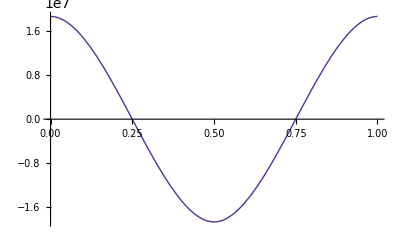

```mathematica
Plot [nonzeroerrpc[x,100],{x,0,1}]
```

```mathematica
nzerrN[x_]=Simplify[nonzeroerrpc[x,N]]
```

3/2 N^2 (1/6 (-4+3 N^2) (1-6 x+6 x^2)-4 N^2 (-1/32+Abs[-1/2+x]^3))

```mathematica
errnonzeroerrpc=Simplify[Simplify[Integrate[nzerrN[x],{x,0,1}]-traprule[nzerrN,2M+1],Assumptions -> M∈Integers]/. M -> (N-2)/4]
```

1

```mathematica
errhatnonzeroerrpc=Simplify[Simplify[traprule[nzerrN,4M+2]-traprule[nzerrN,2M+1],Assumptions -> M∈Integers]/. M -> (N-2)/4, Assumptions -> N > 2]
```

0

### Fluky Function and Its Derivatives

```mathematica
foolB[x_,N_]=1+2nonzeroerrpc[x,N]
```

1+3 N^2 (1/6 (-4+3 N^2) (1-6 x+6 x^2)-4 N^2 (-1/32+Abs[-1/2+x]^3))

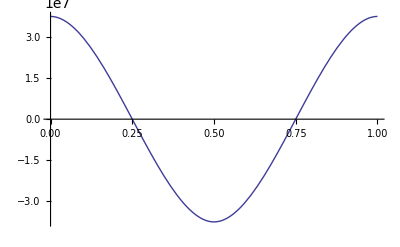

```mathematica
Plot [foolB[x,100],{x,0,1}]
```

```mathematica
Integrate[foolB[x,N],{x,0,1}]
```

1

```mathematica
ffoolB[x_]=foolB[x,N]
```

1+3 N^2 (1/6 (-4+3 N^2) (1-6 x+6 x^2)-4 N^2 (-1/32+Abs[-1/2+x]^3))

```mathematica
BernoulliB[4,x]
```

-1/30+x^2-2 x^3+x^4

```mathematica
Simplify[traprule[ffoolB,N]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/2]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/4]]
```

89

```mathematica
dfoolB[x_,N]=Simplify[-30*N^2*(BernoulliB[1,x]+16N^2(BernoulliB[3,x/2]-1))]
```

-30 N^2 (-1/2+x+2 N^2 (-8+2 x-3 x^2+x^3))

```mathematica
ddfoolB[x_,N]=Simplify[-30*N^2*(1+24 N^2BernoulliB[2,x/2])]
```

-30 N^2 (1+2 N^2 (2-6 x+3 x^2))

```mathematica
dddfoolB[x_,N]=Simplify[-720* N^4BernoulliB[1,x/2]]
```

-360 N^4 (-1+x)

```mathematica
ddddfoolB[x_,N]=-360* N^4
```

-360 N^4

### Total Variation of Fluky Function

```mathematica
node=Solve[dfoolB[x,N]==0,x]
```

{{x→1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2)},{x→1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)},{x→1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)}}

```mathematica
nodex=x/.node
```

{1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2),1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)}

```mathematica
nodex={0,nodex[[2]],nodex[[1]],nodex[[3]],1}
```

{0,1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2),1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1}

```mathematica
nodey=Simplify[foolB[nodex,N]]
```

$Aborted

```mathematica
absdify=Simplify[Abs[Differences[nodey]]]
```

{15/4 Abs[1+2 √(N^2 (-2+N^2))],15/16 Abs[4-4 N^2+N^4+8 √(N^2 (-2+N^2))],15/16 Abs[4-4 N^2+N^4-8 √(N^2 (-2+N^2))],15/4 Abs[1-2 √(N^2 (-2+N^2))]}

```mathematica
totvarfool=Expand[Simplify[Sum[absdify[[i]],{i,1,4}],Assumptions -> N≥ 2]]
```

15/4-(15 N^2)/4+(15 N^4)/16+45/2 N √(-2+N^2)+15/16 Abs[4-4 N^2+N^4-8 N √(-2+N^2)]

### Total Variation of First Derivative of Fluky Function

```mathematica
noded=Solve[ddfoolB[x,N]==0,x]
```

{{x→(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2)},{x→(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2)}}

```mathematica
nodedx=x/.noded
```

{(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2),(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2)}

```mathematica
nodedx={0,nodedx[[1]],nodedx[[2]],1}
```

{0,(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2),(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2),1}

```mathematica
nodedy=Simplify[dfoolB[nodedx,N]]
```

{15 N^2,-(5 (N^2 (-2+N^2))^(3/2))/(√3 N^2),(5 (N^2 (-2+N^2))^(3/2))/(√3 N^2),-15 N^2}

```mathematica
absdifdy=Simplify[Abs[Differences[nodedy]],Assumptions -> N≥2]
```

{5/3 N (9 N+√3 (-2+N^2)^(3/2)),(10 N (-2+N^2)^(3/2))/(√3),5/3 N (9 N+√3 (-2+N^2)^(3/2))}

```mathematica
totvardfool=Simplify[Sum[absdifdy[[i]],{i,1,3}],Assumptions -> N≥2]
```

10/3 N (9 N+2 √3 (-2+N^2)^(3/2))

```mathematica
conetaufool=Simplify[totvardfool/totvarfool]
```

(32 N (9 N+2 √3 (-2+N^2)^(3/2)))/(9 (4-4 N^2+N^4+24 N √(-2+N^2)+Abs[4-4 N^2+N^4-8 N √(-2+N^2)]))

### Total Variation of Second Derivative of Fluky Function

```mathematica
nodedd=Solve[dddfoolB[x,N]==0,x]
```

{{x→1/2}}

```mathematica
nodeddx=x/.nodedd
```

{1/2}

```mathematica
nodeddx={0,nodeddx[[1]],1}
```

{0,1/2,1}

```mathematica
nodeddy=Simplify[ddfoolB[nodeddx,N]]
```

{-30 N^2 (1+N^2),15 N^2 (-2+N^2),-30 N^2 (1+N^2)}

```mathematica
absdifddy=Simplify[Abs[Differences[nodeddy]]]
```

{45 Abs[N]^4,45 Abs[N]^4}

```mathematica
totvarddfool=Simplify[Sum[absdifddy[[i]],{i,1,2}],Assumptions -> N∈Integers]
```

90 N^4

### A Slightly Different Function

```mathematica
badfoolB2[x_,N_]=15*N^2BernoulliB[2,x]
```

15 N^2 (1/6-x+x^2)

```mathematica
Integrate[badfoolB2[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB2[i/N,N],{i,0,N-1}]/N
```

5/2

```mathematica
trapNov2=Sum[badfoolB2[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

10

```mathematica
errhat=(trapN - trapNov2)/3
```

-5/2

```mathematica
badfoolB4[x_,N_]=15*N^4BernoulliB[4,x]
```

15 N^4 (-1/30+x^2-2 x^3+x^4)

```mathematica
Integrate[badfoolB4[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB4[i/N,N],{i,0,N-1}]/N
```

-1/2

```mathematica
trapNov2=Sum[badfoolB4[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

-8

```mathematica
errhat=(trapN - trapNov2)/3
```

5/2

## Bernoulli Polynomials

```mathematica
Factor[BernoulliB[3,x]]
```

1/2 (-1+x) x (-1+2 x)

```mathematica
Factor[D[BernoulliB[4,x],x]]
```

2 (-1+x) x (-1+2 x)

```mathematica
Factor[BernoulliB[5,x]]
```

1/6 (-1+x) x (-1+2 x) (-1-3 x+3 x^2)